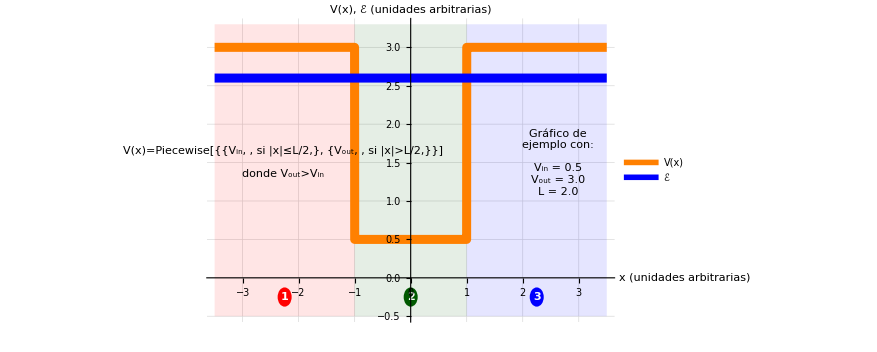
Pozo finito de potencial, caso (b).

Este archivo muestra cómo resolver la ecuación de Schrödinger independiente del tiempo (ESIT) para un pozo finito de potencial cuando la energía de la partícula es mayor que el mínimo del potencial, pero menor que el máximo. 

-Graphics-

Para cada región indicada en la figura tendremos una ESIT de la forma 

	-ℏ^2/(2m)(ⅆ^2 ψ_j)/(ⅆ x^2)+V_j ψ_j= ℰ ψ_j, 	donde 	j=1,2,3, 	V_1=V_3=V_out 	y	V_2=V_in.

Estas ecuaciones son equivalentes a 	ψ''_j(x)+k_j^2 ψ_j(x)=0,	donde	k_1 | = | √((2m)/ℏ^2(ℰ-V_out)) | = | k_out,
k_2 | = | √((2m)/ℏ^2(ℰ-V_in)) | = | k_in,
k_3 | = | √((2m)/ℏ^2(ℰ-V_out)) | = | k_out. 

Las soluciones para cada región serán de la forma 	ψ_j(x)=A_j ⅇ^(ⅈ k_j x) + B_j ⅇ^(-ⅈ k_j x),	donde los coeficientes A_j y B_j son incógnitas a determinar. 
Note que si la energía ℰ es menor que alguno de los V_j, ocurrirá que el respectivo k_j será un número puramente imaginario: k_j→ⅈ γ_j.

Para simplificar la descripción, hay algunos parámetros auxiliares que usaremos en ocasiones: 

	ΔV | = | V_out-V_in | : | "profundidad" del pozo.    										
Δℰ | = | ℰ-V_in | : | indica cuánto sobresale la energía ℰ por encima del fondo del pozo.           	
η | = | Δℰ/ΔV | : | ubicación de la energía ℰ relativa a la profundidad del pozo.     			
  |   |   |   | Por ejemplo, η=1/2 indica que ℰ  está exactamente a la mitad entre V_in y V_out.    
λ_dB | = | √((2 π^2 ℏ^2)/(m Δℰ)) | : | longitud de onda de de Broglie de la partícula, tomando Δℰ como referencia.
  |   |   |   | •  Imagine que la energía cinética (p^2/2m) de la partícula fuese Δℰ.
  |   |   |   | • Entonces, p=√(2m Δℰ).            							
  |   |   |   | • La hipótesis de de Broglie dice que p=ℏk, donde k=2π/λ_dB.         
  |   |   |   | • Despejando, se obtiene que λ_dB=√((2 π^2 ℏ^2)/(m Δℰ)).    				
Λ | = | L/λ_dB | : | ancho del pozo, pero expresado en múltiplos de λ_dB.       				   	

Con estas sustituciones, podemos escribir también que	k_in | = | √((2m)/ℏ^2 Δℰ) | = | √((2m ΔV)/ℏ^2)√η | ,
k_out | = | √((2m)/ℏ^2(Δℰ-ΔV)) | = | √((2m ΔV)/ℏ^2)√(η-1) | ,
Λ | = | L √(m/(2 π^2 ℏ^2)Δℰ) | = | L/(2π)√((2m ΔV)/ℏ^2)√η | .

Condiciones de continuidad.

Se impone que la función de onda sea continua para que la probabilidad de encontrar a la partícula en una zona no tenga vacíos físicamente inadmisibles. 

Dado que el potencial V(x) es finito en todo su dominio, la derivada de la función de onda también es continua. 

Los puntos “problemáticos” son x=±L/2, que es donde el potencial exhibe discontinuidades y, a causa de ello, es también donde separamos la función de onda en tramos. Impondremos las condiciones de continuidad en esos puntos x=±L/2: 

	ψ_1^(-L/2) | = | ψ_2^(-L/2)  | 		⇒		 | A_1 ⅇ^(-1/2 ⅈ L k_out)+B_1 ⅇ^(1/2 ⅈ L k_out) | = | A_2 ⅇ^(-1/2 ⅈ L k_in)+B_2 ⅇ^(1/2 ⅈ L k_in)
ψ_1^′(-L/2) | = | ψ_2^′(-L/2)  | 		⇒		 | ⅈ A_1 k_out ⅇ^(-1/2 ⅈ L k_out)-ⅈ B_1 k_out ⅇ^(1/2 ⅈ L k_out) | = | ⅈ A_2 k_in ⅇ^(-1/2 ⅈ L k_in)-ⅈ B_2 k_in ⅇ^(1/2 ⅈ L k_in)
ψ_2^(+L/2) | = | ψ_3^(+L/2)  | 		⇒		 | A_2 ⅇ^(1/2 ⅈ L k_in)+B_2 ⅇ^(-1/2 ⅈ L k_in) | = | A_3 ⅇ^(1/2 ⅈ L k_out)+B_3 ⅇ^(-1/2 ⅈ L k_out)
ψ_2^′(+L/2) | = | ψ_3^′(+L/2)  | 		⇒		 | ⅈ A_2 k_in ⅇ^(1/2 ⅈ L k_in)-ⅈ B_2 k_in ⅇ^(-1/2 ⅈ L k_in) | = | ⅈ A_3 k_out ⅇ^(1/2 ⅈ L k_out)-ⅈ B_3 k_out ⅇ^(-1/2 ⅈ L k_out)

Así, estas cuatro ecuaciones forman un sistema de ecuaciones lineales para los coeficientes A_1,B_1,A_2,B_2,A_3,B_3. Otras ecuaciones y/o condiciones adicionales se verán caso a caso.

Caso (b): V_out>ℰ>V_in

Aquí ocurrirá que 	k_1=k_3=ⅈγ_out 	y 	k_2=k_in, 	donde	Piecewise[{{k_in=√((2m)/ℏ^2(ℰ-V_in)), ,}, {γ_out=√((2m)/ℏ^2(V_out-ℰ)), .}}]
Es decir, habrá comportamiento oscilatorio en la Región 2 y comportamiento exponencial en las Regiones 1 y 3. 

	ψ_1 | = | A_1 ⅇ^-γ_outx | + | B_1 ⅇ^(γ_out x) | ,
ψ_2 | = | A_2 ⅇ^(ⅈ k_in^x)   | + | B_2 ⅇ^(ⅈ k_in^x)  | ,
ψ_3 | = | A_3 ⅇ^-γ_outx | + | B_3 ⅇ^(γ_out x) | .

Las exponenciales reales pueden converger asintóticamente a cero o diverger cuando nos alejamos del origen. Considerando que γ_out es positivo: 
 	•  En la Región 1, ⅇ^-γ_outx diverge cuando x→-∞. 
 	•  En la Región 3, ⅇ^(+γ_outx) diverge cuando x→+∞. 

Si imponemos de antemano que A_1=B_3=0, no tendremos que lidiar con ninguna de esas divergencias. Con ello, ya vemos que la función de onda tendrá comportamiento oscilatorio en la Región 2 y comportamiento evanescente en las Regiones 1 y 3:  

	ψ_1 | = | B_1 ⅇ^(γ_out x) |   |   | ,
ψ_2 | = | A_2 ⅇ^(ⅈ k_in^x)   | + | B_2 ⅇ^(-ⅈ k_in^x)  | ,
ψ_3 | = | A_3 ⅇ^-γ_outx |   |   | .

Tenemos un grado de confinamiento. Cuando un estado se encuentra confinado debido a que su energía no supera el valor del potencial salvo en regiones acotadas diremos que este estado es un estado ligado (bound states). Los del caso (a), en cambio, suelen llamarse estados de scattering.

Puede notar también que k_in^2+γ_out^2=(2m ΔV)/ℏ^2

Paridad de las eigenfunciones. 

Este pozo de potencial, en la forma en que fue definido, es una función par ya que  V(-x)=V(x). Debido a ello, el operador hamiltoniano conmuta con el operador de paridad. Y nosotros sabemos que dos observables que conmuten pueden escribirse con los mismos estados propios. 

	[Ĥ,Π̂]=𝕆̂ 	⇔	∃{Ψ_n}:    Ĥ Ψ_n=ℰ_n Ψ_n      ∧      Π̂ Ψ_n=s_n Ψ_n,       s_n=±1.

Debido a lo anterior, las funciones de onda propias de este pozo podrán categorizarse en eigenfunciones pares e impares. 
Recordemos que habíamos construido las funciones de onda por tramos, 

	ψ_1 | = | B_1 ⅇ^(γ_out x) |   |   | ,
ψ_2 | = | A_2 ⅇ^(ⅈ k_in^x)   | + | B_2 ⅇ^(-ⅈ k_in^x)  | ,
ψ_3 | = | A_3 ⅇ^-γ_outx |   |   | .	que también podemos
expresar como	Ψ(x)=Piecewise[{{B_1 ⅇ^(γ_out x), x<-L/2}, {A_2 ⅇ^(ⅈ k_in^x)+B_2 ⅇ^(-ⅈ k_in^x), -L/2≤x<L/2}, {A_3 ⅇ^-γ_outx, L/2<x}}]

Si tomamos en cuenta la opción de paridad, 
	Ψ_par(-x)=+Ψ_par(x) | 	⇒	 | Ψ_par(x)=Piecewise[{{B_1 ⅇ^(γ_out x), x<-L/2}, {2 A_2 cos(k_in^x), -L/2≤x<L/2}, {B_1 ⅇ^-γ_outx, L/2<x}}]
y |   |  
Ψ_impar(-x)=-Ψ_impar(x) | 	⇒	 | Ψ_impar(x)=Piecewise[{{-B_1 ⅇ^(γ_out x), x<-L/2}, {2ⅈ A_2 sin(k_in^x), -L/2≤x<L/2}, {B_1 ⅇ^-γ_outx, L/2<x}}]

Vemos que la paridad puede aprovecharse a favor para eliminar incógnitas. Si bien ahora tenemos dos ramas, pares e impares, cada rama solo tiene 2 incógnitas en vez de 4. Incluso podemos simplificar esto aún más al reabsorber las constantes A_2 y B_1 en nuevas constantes: 

	Ψ_par(x)=Piecewise[{{ℬ_par ⅇ^(γ_out x), x<-L/2}, {𝒜_par cos(k_in^x), -L/2≤x<L/2}, {ℬ_par ⅇ^-γ_outx, L/2<x}}]			Ψ_impar(x)=Piecewise[{{-ℬ_impar ⅇ^(γ_out x), x<-L/2}, {𝒜_impar sin(k_in^x), -L/2≤x<L/2}, {ℬ_impar ⅇ^-γ_outx, L/2<x}}]


En el caso (a), el potencial es simétrico, pero el contexto fue interpretado como asimétrico: la partícula venía desde una dirección específica y usamos esa amplitud incidente como referencia. Es por ello que no utilizamos la paridad para analizar ese caso. No obstante, si no nos hubiera importado la interpretación y solo hubiésemos querido calcular soluciones, también podríamos  haber aplicado las simplificaciones debido a la simetría de paridad.

Sistemas de ecuaciones y condiciones sobre la energía.

Ahora tendremos un sistema de ecuaciones para la rama par y otro para la rama impar. Incorporando también las modificaciones k_out→ⅈ γ_out ,  A_1→0 y B_3→0, tendremos

	(ℬ_par ⅇ^(-(L γ_out)/2) | = | 𝒜_par cos((L k_in)/2)
γ_out ℬ_par ⅇ^(-(L γ_out)/2) | = | k_in 𝒜_par sin((L k_in)/2)
𝒜_par cos((L k_in)/2) | = | ℬ_par ⅇ^(-(L γ_out)/2)
-k_in 𝒜_par sin((L k_in)/2) | = | -γ_out ℬ_par ⅇ^(-(L γ_out)/2))	y	(-ℬ_impar ⅇ^(-(L γ_out)/2) | = | -𝒜_impar sin((L k_in)/2)
-γ_out ℬ_impar ⅇ^(-(L γ_out)/2) | = | k_in 𝒜_impar cos((L k_in)/2)
𝒜_impar sin((L k_in)/2) | = | ℬ_impar ⅇ^(-(L γ_out)/2)
k_in 𝒜_impar cos((L k_in)/2) | = | -γ_out ℬ_impar ⅇ^(-(L γ_out)/2))	

En ambas ramas se puede notar que las últimas dos ecuaciones son equivalentes a las dos primeras ecuaciones, de modo que los sistemas tienen dos ecuaciones efectivas: 

	(𝒜_par cos((L k_in)/2) | = | ℬ_par ⅇ^(-(L γ_out)/2)
k_in 𝒜_par sin((L k_in)/2) | = | γ_out ℬ_par ⅇ^(-(L γ_out)/2))	y	(𝒜_impar sin((L k_in)/2) | = | ℬ_impar ⅇ^(-(L γ_out)/2)
k_in 𝒜_impar cos((L k_in)/2) | = | -γ_out ℬ_impar ⅇ^(-(L γ_out)/2))	

Cada sistema solo tiene dos ecuaciones y dos incógnitas. Se pueden representar matricialmente como 	M_s·(v⃗)_s=OverVector[0],	donde:
	• El subíndice s denota la paridad, par o impar. 
	    Usaremos s como el nombre de la paridad o como un signo ± indistintamente. 
	• M_s es la matriz de coeficientes, M_par=(ⅇ^((L γ_out)/2) cos((L k_in)/2) | -1
k_in ⅇ^((L γ_out)/2) sin((L k_in)/2) | -γ_out)	y	M_impar=(ⅇ^((L γ_out)/2) sin((L k_in)/2) | -1
k_in ⅇ^((L γ_out)/2) cos((L k_in)/2) | γ_out).
	• (v⃗)_s es el vector que contiene a las incógnitas, (v⃗)_s=(𝒜_s
ℬ_s).

Ambos son sistemas homogéneos cuya solución es (v⃗)_s=OverVector[0] (solución trivial). Esta solución es muy poco conveniente porque nos dice que la función de onda, básicamente, no existe. ¿Cómo evadimos la solución trivial? Si imponemos que el sistema de ecuaciones sea linealmente dependiente, entonces podremos escribir algunas de las incógnitas en función de la otras de forma no trivial. La dependencia lineal se puede forzar imponiendo que 

	det(M_s)=0.	 

Esto se debe a que det(M_s)=0 implica que M_s no es invertible, de modo que la ruta v⃗=M_s^-1·OverVector[0]=OverVector[0] no sería matemáticamente válida. Así se evade la solución trivial. 

(   Usando operadores lógicos, |   |   |   |  
  |   |   |   |  
	((v⃗)_s≠OverVector[0])^(Queremos:)   ∧  (M_s(v⃗)_s=OverVector[0])^(Tenemos:)  | 	⇔	 | (v⃗)_s≠OverVector[0]   ∧ ((v⃗)_s=M_s^-1 OverVector[0]  ∨  ∄M_s^-1) |   |  
  | 	⇔	 | (v⃗)_s≠OverVector[0]   ∧ ((v⃗)_s=OverVector[0]  ∨  det(M_s)=0) |   |  
  | 	⇔	 | ((v⃗)_s≠OverVector[0] ∧ (v⃗)_s=OverVector[0])_Contradicción ∨ ((v⃗)_s≠OverVector[0] ∧ det(M_s)=0) | 	⇔	 | (v⃗)_s≠OverVector[0] ∧ det(M_s)=0)


Si no hubiéramos considerado la simetría de paridad, el sistema de ecuaciones modificado con k_out→ⅈ γ_out ,  A_1→0 y B_3→0  sería
	B_1 ⅇ^(-(L γ_out)/2) | = | A_2 ⅇ^(-1/2 ⅈ L k_in)+B_2 ⅇ^(1/2 ⅈ L k_in)
B_1 γ_out ⅇ^(-(L γ_out)/2) | = | ⅈ A_2 k_in ⅇ^(-1/2 ⅈ L k_in)-ⅈ B_2 k_in ⅇ^(1/2 ⅈ L k_in)
A_2 ⅇ^(1/2 ⅈ L k_in)+B_2 ⅇ^(-1/2 ⅈ L k_in) | = | A_3 ⅇ^(-(L γ_out)/2)
ⅈ A_2 k_in ⅇ^(1/2 ⅈ L k_in)-ⅈ B_2 k_in ⅇ^(-1/2 ⅈ L k_in) | = | -A_3 γ_out ⅇ^(-(L γ_out)/2)

Hay 4 ecuaciones y 4 incógnitas, B_1,A_2,B_2,A_3. En este caso, el sistema también se puede representar como	M·v⃗=OverVector[0],	solo que los vectores y matrices serán de dimensión 4. Y también se debe imponer det(M)=0 para evitar la solución trivial. Al final, se llega a los mismos resultados que considerando la paridad, pero el camino es un poco más largo.

Discretización de la energía.

Acabamos de ver que se necesita imponer det(M_s)=0. Para el sistema de ecuaciones de este caso, 

	(det(M_par)=0 | 	⇒ 	 | k_in sin((L k_in)/2)==γ_out cos((L k_in)/2)
  |   |  
det(M_impar)=0  | 	⇒ 	 | γ_out sin((L k_in)/2)==-k_in cos((L k_in)/2)   )	, donde	Piecewise[{{k_in=√((2m)/ℏ^2 Δℰ), ,}, {γ_out=√((2m)/ℏ^2(ΔV-Δℰ)), .}}]

Todos los parámetros que aparecen en esta imposición se pueden resumir en: 
 	• m, la masa de la partícula. Es fija. 
 	• L, el ancho del pozo. Si bien se puede ajustar externamente, es fija para un pozo dado.
   	• ΔV=V_out-V_in, la profundidad del pozo. También es fija para un pozo dado (y ajustable solo externamente).
 	• Δℰ=ℰ-V_in, la energía de la partícula por encima del fondo del pozo. Como ℰ es variable, Δℰ también lo es. 

El único parámetro variable que tiene cada det(M_s)=0 es la energía. Es decir, los ceros de det(M_s)=0 constituyen un listado de restricciones sobre los posibles valores que puede adoptar la energía del sistema. Dado que estos ceros suelen aparecer en cantidades discretas, podemos decir que la energía queda sometida a condiciones que imponen su discretización. 

¿Y si un valor específico de energía no cumple con det(M)=0? Pues, dicha energía está condenada a tener funciones de onda nula:

	M_s·(v⃗)_s=OverVector[0]	⇒	(det(M_s)≠0  ∧  (v⃗)_s=OverVector[0])  ∨ (det(M_s)=0).
 	• Si la energía no satisface det(M_s)=0, termina forzando (v⃗)_s=OverVector[0] (solución nula). 
 	• Si la energía sí cumple con det(M_s)=0, ahí la solución podría no ser nula.  

No hay más opciones. La energía debe cumplir con det(M_s)=0. Y como ahora las ecuaciones serán linealmente dependientes, se puede escribir los ℬ_s en función de los 𝒜_s:

	ℬ_par=𝒜_par ⅇ^((L γ_out)/2)cos((k_in L)/2)	y	ℬ_impar=𝒜_impar ⅇ^((L γ_out)/2)sin((k_in L)/2) .

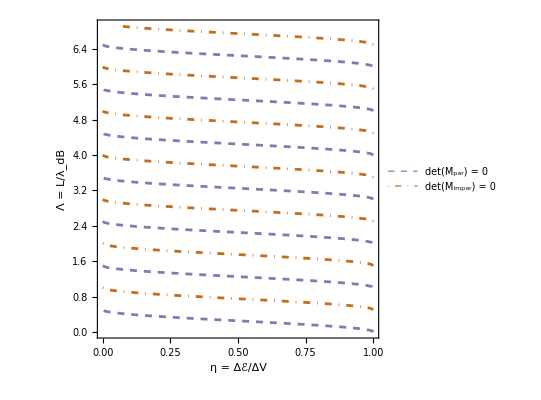
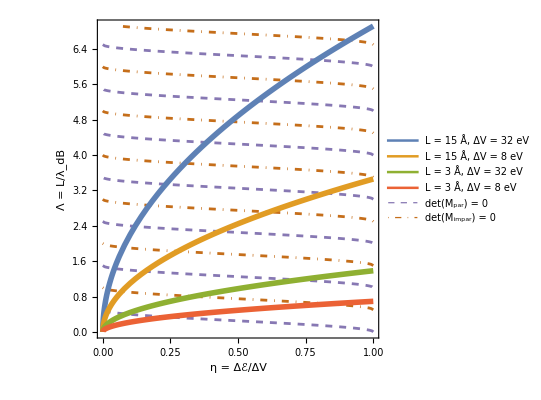
¿Cómo determinamos las energías desde det(M)= 0?
 
Tenemos dos condiciones por separado, Piecewise[{{Pares |       :, k_in sin((L k_in)/2)==γ_out cos((L k_in)/2)}, {Impares | :, k_in cos((L k_in)/2)==-γ_out sin((L k_in)/2)}}] 
y en ninguna de ellas podemos despejar algebraicamente los valores de energía ya que ambas son ecuaciones trascendentales. Toda búsqueda debe ser numérica. Por ello, debemos simplificar las expresiones e intentar usar variables adimensionales. Los parámetros auxiliares del comienzo sirven para este propósito, dejando ambas condiciones como

	Pares | : | √(1-η)cos(π Λ) | = | √η sin(π Λ),
Impares | : | √(1-η)sin(π Λ) | = | -√ηcos(π Λ),   		donde  Λ=L/(2π)√((2m ΔV)/ℏ^2)√η,	

o bien como F_par(η)=0   y   F_impar(η)=0, donde

	     F_par(η) | = | √(1-η)cos( 𝒸 √η) | - | √η sin(𝒸 √η) | ,
F_impar(η) | = | √(1-η)sin(𝒸 √η) | + | √η cos(𝒸 √η) | ,   		siendo  𝒸=L/2 √((2m ΔV)/ℏ^2).	

Estas simplificaciones nos permiten empezar la búsqueda. 

 	◦ Las ecuaciones F_par(η)=0   y   F_impar(η)=0 imponen condiciones sobre η y Λ, que se grafican a continuación:

	-Graphics-

  	  	
  	 ◦ Dadosm, L, ΔVfijos, calcule  𝒸=L/2 √((2m ΔV)/ℏ^2).  Luego:
  |   | ℰ | 	 | • | Tome un valorℰde energía. 						
  |   | ↓ |   |   |  
  |   | Δℰ |   | • | Useℰpara calcularΔℰ.							
  |   | ↓ |   |   |  
                                ΔV | → | η |   | • | UseΔℰpara calcular η.							
  |   | ↓ |   |   |  
(m,L,ΔV) →  𝒸   | → | Λ |   | • | Useηpara calcularΛ = 𝒸/π √η.       					
  |   | ↓ |   |   |  
  |   | ( η , Λ ) |   | • | Los valores obtenidos deηyΛ forman el punto (η,Λ)	
  |   | ↓ |   |   |  
  |   | Compare |   | • | ¿Está (η,Λ) contenido en alguna de las curvas?     		
  |   | ↓ |   |   | 	Piecewise[{{Sí, : es una energía permitida}, {No, : no es una energía permitida (solución trivial)}}]
  |   | Repita |   | • | Repita para otros valores de energía.     				 
  		
 	◦ De este modo, las energías permitidas están en las intersecciones de las líneas del gráfico anterior con las de la curva
		Λ(η; L,ΔV,m) =  L/(2π)√((2m ΔV)/ℏ^2)√η.	
	-Graphics-
	
	◦ Ya tenemos una idea gráfica de cómo se comportan estas energías, ¿pero cómo determinamos numéricamente esas intersecciones? 
	 	• F_par(η)   y   F_impar(η) son no lineales. No parece sencillo encontrar sus ceros. 
		• No obstante, la sustitución intermedia η=sin^2 φ  (con 0≤φ≤π/2) es de mucha ayuda: 
			      f_par(φ) | = | F_par(η→sin^2 φ) | = | cos(φ+ 𝒸 sin(φ)), |  
f_impar(φ) | = | F_impar(η→sin^2 φ) | = | sin(φ+ 𝒸 sin(φ)), |        y ambas son más fáciles de trabajar así. 	    
		
		• Los respectivos ceros de ambas funciones están en Piecewise[{{φ_(𝒿,par)+𝒸 sin(φ_(𝒿,par))=, (2𝒿+1)π/2}, {φ_(𝒿,impar)+𝒸 sin(φ_(𝒿,impar))=, (2𝒿)π/2}}], con 𝒿∈ℤ.
			– Se puede ver un cierto mismatch entre la paridad de la función y el número que multiplica al π/2.
			– Por lo mismo, no se debe confundir paridad de una función con paridad de un número cuántico. 
			
		• Definamos un único número n para ambos casos: 
			φ_n+𝒸 sin(φ_n)=n π/2, 	 donde  	 n∈ℤ 	 y 	 Piecewise[{{Ψ_(n=(2𝒿+1)), son funciones pares,}, {Ψ_(n=(2𝒿)), son funciones impares.}}]
		
		• Así, debemos encontrar los φ_n tales que φ_n+𝒸 sin(φ_n)=n π/2 y usamos esos φ_n para calcular las energías.		
		
		• Algorítmicamente:
(m,L,ΔV)→𝒸                                 |     | • | Dados m, L y ΔV, Calcule 𝒸=L/2 √((2m ΔV)/ℏ^2)   						
↓ |   |   |  
φ_n+𝒸 sin(φ_n)=n π/2 |   | • | Busque valores φ_n∈(0,π/2] tales que φ_n+𝒸 sin(φ_n)=n π/2,con n∈ℤ.            
↓ |   |   |  (φ_n=0 se debe descartar, como se ve más adelante)
    φ_n   y/o   φ_(𝒿,s)  |   | • | Piecewise[{{– Los n impares generan soluciones pares, φ_(𝒿,par), con 𝒿=(n-1)/2.}, {– Los n pares generan soluciones impares, φ_(𝒿,impar),con 𝒿=n/2.}}]            
↓ |   |   |  
   η_n   y/o   η_(𝒿,s) |   | • | Calcule η_n=sin^2(φ_n) o bien η_(𝒿,s)=sin^2(φ_(𝒿,s)), donde s=Piecewise[{{par., }, {impar., }}]              
↓ |   |   |  
   Δℰ_n   y/o   Δℰ_(𝒿,s) |   | • | Calcule Δℰ_n=η_n ΔV, o bien Δℰ_(𝒿,s)=η_(𝒿,s)ΔV.       					
↓ |   |   |  
   ℰ_n   y/o   ℰ_(𝒿,s) |   | • | Calcule ℰ_n=Δℰ_n+V_in,o bien ℰ_(𝒿,s)=Δℰ_(𝒿,s)+V_in.            				
↓ |   |   |  
   Ψ_n   y/o   Ψ_(𝒿,s) |   | • |  Use las energías y construya los Ψ_n(x)  o  los Ψ_(𝒿,s)(x).

¿Cuántos estados ligados tendrá el sistema?
	
Dado que 0≤η≤1, la definición η=sin^2(φ),  requiere 0≤φ≤π/2. 

	◦ Como φ_n≥0, los n no pueden ser negativos. 
	◦ Pero n tampoco puede ser igual a cero:
		 (n=0)_(n par,
Ψ_n impar) ⇒ φ_0=0 ⇒ η_0=0 ⇒ k_in=0 ∧ γ_out=0 ⇒ (Ψ_0=constante)_(Función constante
e impar al mismo tiempo
solo puede ser cero)
	◦ Por lo tanto, n≥1. Ahora nos falta una cota superior para n.
	◦ Los ceros están en  φ_n+𝒸 sin(φ_n)=n π/2. Equivalentemente, n=2/π(φ_n+𝒸 sin(φ_n)).
	◦ Notemos que la función n(ϕ)=2/π(ϕ+𝒸 sin(ϕ)) es creciente en 0≤ϕ≤π/2, teniendo en cuenta que 𝒸>0:
		ⅆn/ⅆϕ=2/π(1+𝒸 cos(ϕ))>0, 	ya que    cos(ϕ)>0    en el intervalo [0,π/2]. 
	◦ Por lo tanto, dado un valor fijo de 𝒸, el máximo de n estará en ϕ=π/2:
		n_max=n(ϕ=π/2)=2/π(π/2+𝒸 sin(π/2)) = 1+(2𝒸)/π. 	
	◦ Pero n_max debe ser un número entero y (2𝒸)/π puede no serlo. Podemos forzarlo como
		n_max=⟦1+(2𝒸)/π⟧ =⌈(2𝒸)/π⌉, donde ⟦x⟧ denota la parte entera de x  y  ⌈x⌉ es la función techo (ceiling).  		
	
	◦ Con esto, concluimos que 1≤n≤⌈(2𝒸)/π⌉ y que existirán n_bnd=⌈(2𝒸)/π⌉ estados ligados.
	
	◦ Para interpretar mejor este número de estados ligados: 
		• Imagine que el pozo tuviera su propia longitud de onda de de Broglie (λ_ΔV) correspondiente a la energía ΔV.
		• Entonces, λ_ΔV=(2π)/(k_(E=ΔV))=(2π)/(√(2m ΔV / ℏ^2)). Equivalentemente, √((2m ΔV)/ℏ^2)=(2π)/λ_ΔV.
		• En consecuencia, n_bnd=⌈(2𝒸)/π⌉=⌈2/π L/2 √((2m ΔV)/ℏ^2)⌉=⌈2/π L/2(2π)/λ_ΔV⌉=⌈(2L)/λ_ΔV⌉=⌈L/(λ_ΔV / 2)⌉.

Este número n_bnd=⌈L/(λ_ΔV / 2)⌉ nos recuerda a la relación de armónicos en una cuerda de guitarra: los armónicos permitidos eran aquellos donde la longitud de la cuerda era un número entero de semilongitudes de onda. 
Aqu.08í tenemos que esa razón entre el ancho del pozo y semilongitudes de onda de de Broglie “del pozo” es quien nos dice cuántos estados ligados habrá.



* Para ver los gráficos interactivos, ejecute la siguiente celda y vaya al final del archivo.

```mathematica
Remove["Global`*"];  
$Assumptions=And@@Thread[{Subscript[k, in],Subscript[k, out],Subscript[Κ, P],Subscript[γ, in],Subscript[γ, out],L,ℒ,Λ,Subscript[λ, P],Subscript[λ, dB],m,ℏ,ℰ,η,Subscript[V, in],Subscript[V, out],ΔV,Δ𝒱,𝒜^◦,𝓂,𝓈,ℯ𝒱,𝒸}>0]&&Δℰ>0&&0≤η≤1&&0≤φ≤π/2;

(* Funciones de onda posibles. *)
Subscript[ψ, j_][x_]:=Subscript[A, j] ⅇ^(ⅈ Subscript[κ, j] x)+Subscript[B, j] ⅇ^(-ⅈ Subscript[κ, j] x);


(* Reducción de parámetros. *)
(* ΔV = Subscript[V, out] - Subscript[V, in], "profundidad" del pozo. *)
Reduccion={
	Subscript[k, in]->√((2m)/ℏ^2(ℰ-Subscript[V, in])),
	Subscript[k, out]->√((2m)/ℏ^2(ℰ-Subscript[V, out])),
	Subscript[γ, in]->√((2m)/ℏ^2(Subscript[V, in]-ℰ)),
	Subscript[γ, out]->√((2m)/ℏ^2(Subscript[V, out]-ℰ)),
	ℰ->Δℰ+Subscript[V, in],
	Subscript[V, out]->ΔV+Subscript[V, in],
	Δℰ->η ΔV,
	Subscript[λ, dB]->√((2 π^2 ℏ^2)/(m Δℰ)),
	L->Λ Subscript[λ, dB]		
};


(*"
Para gráficos, consideremos un electrón en un pozo que tiene unos cuantos årmströng de ancho y unos cuantos electronvolts de profundidad. Podemos ir cambiando L y ΔV.
"*)
Numeros={
		Subscript[k, in]->√((2m)/ℏ^2(ℰ-Subscript[V, in])),
		Subscript[k, out]->√((2m)/ℏ^2(ℰ-Subscript[V, out])),
		Subscript[γ, in]->√((2m)/ℏ^2(Subscript[V, in]-ℰ)),
		Subscript[γ, out]->√((2m)/ℏ^2(Subscript[V, out]-ℰ)),
		Subscript[λ, dB]->√((2 π^2 ℏ^2)/(m Δℰ)),
		ℰ->Δℰ+Subscript[V, in],
		Subscript[V, out]->ΔV+Subscript[V, in],
		Δℰ->η ΔV,
		c->299792458 𝓂/𝓈,
		ℏ->6.62607015/(2π)×10^-34 𝒥 𝓈,
		𝒥->ℯ𝒱/(1.60217663×10^-19),
		m->0.511 ×10^6 ℯ𝒱/c^2,
		𝓂->𝒜^◦/10^-10,
		L->ℒ 𝒜^◦,                                       (* ℒ: Ancho del pozo, pero medido en årmströngs. *)
		ΔV->Δ𝒱 ℯ𝒱		             (* Δ𝒱: profundidad del pozo, pero medido en electronvolts. *)
};

(* Funciones solo para ayudar en la presentación de resultados. *)
TsT[args__]:=TraditionalForm[StringRiffle[ToString[#,TraditionalForm]&/@{args}]]

(* Condiciones de continuidad. *)
Continuidad={
			Subscript[ψ, 1][-L/2]==Subscript[ψ, 2][-L/2],
			Subscript[ψ, 1]'[-L/2]==Subscript[ψ, 2]'[-L/2],
			Subscript[ψ, 2][L/2]==Subscript[ψ, 3][L/2],
			Subscript[ψ, 2]'[L/2]==Subscript[ψ, 3]'[L/2]
			};

SubsB={Subscript[κ, 1]->ⅈ Subscript[γ, out],Subscript[κ, 2]->Subscript[k, in],Subscript[κ, 3]->ⅈ Subscript[γ, out],Subscript[A, 1]->0,Subscript[B, 3]->0};
ReduccionSimple={Subscript[k, in]->√((2m)/ℏ^2 Δℰ),Subscript[γ, out]->√((2m)/ℏ^2(ΔV-Δℰ)),Δℰ->η ΔV};

(* Sin considerar paridad: *)
Subscript[Eqs, b]=Continuidad//.SubsB;
Subscript[v, b]={Subscript[B, 1], Subscript[A, 2], Subscript[B, 2], Subscript[A, 3]};

(* Podemos expresar el sistema de ecuaciones como M·v⃗=b⃗, donde: *)
{Subscript[b, b],Subscript[M, b]}=Normal[CoefficientArrays[Subscript[Eqs, b],Subscript[v, b]]];
Subscript[b, b]=-Subscript[b, b];             (* CoefficientArrays construye como Subscript[M, b].Subscript[v, b]+Subscript[b, b]=0. Nosotros usamos Subscript[M, b].Subscript[v, b]=Subscript[b, b]. *)

(* El sistema es homogéneo. Si lo resolvemos inmediatamente, caeremos en la solución trivial. *)
Subscript[S, b]=Flatten[FullSimplify[Solve[Subscript[Eqs, b],Subscript[v, b]]]];

TsT["Caso (b): V_out>ℰ>V_in (sin considerar paridad)\nSistema matricial M·v⃗ = b⃗\n",
	Subscript[M, b]·{Subscript[v, b]}ᵀ=={Subscript[b, b]}ᵀ,"\n\nSoluciones (?):\n",Flatten["\n"Subscript[S, b]]]


(* Si consideramos la paridad, se simplifican las ecuaciones. *)
Subscript[ζ, 1][x_]:=Subscript[ℬ, par] ⅇ^(Subscript[γ, out] x);
Subscript[ζ, 2][x_]:=Subscript[𝒜, par] Cos[Subscript[k, in] x];
Subscript[ζ, 3][x_]:=Subscript[ℬ, par] ⅇ^(-Subscript[γ, out]x);

Subscript[ξ, 1][x_]:=-Subscript[ℬ, impar] ⅇ^(Subscript[γ, out] x)
Subscript[ξ, 2][x_]:=Subscript[𝒜, impar] Sin[Subscript[k, in] x];
Subscript[ξ, 3][x_]:=Subscript[ℬ, impar] ⅇ^(-Subscript[γ, out]x);

Subscript[Eqs, b,par]=FullSimplify[{
			Subscript[ζ, 1][-L/2]==Subscript[ζ, 2][-L/2],
			Subscript[ζ, 1]'[-L/2]==Subscript[ζ, 2]'[-L/2],
			Subscript[ζ, 2][L/2]==Subscript[ζ, 3][L/2],
			Subscript[ζ, 2]'[L/2]==Subscript[ζ, 3]'[L/2]
			}];

Subscript[Eqs, b,impar]=FullSimplify[{
			Subscript[ξ, 1][-L/2]==Subscript[ξ, 2][-L/2],
			Subscript[ξ, 1]'[-L/2]==Subscript[ξ, 2]'[-L/2],
			Subscript[ξ, 2][L/2]==Subscript[ξ, 3][L/2],
			Subscript[ξ, 2]'[L/2]==Subscript[ξ, 3]'[L/2]
			}];

Subscript[v, b,par]={Subscript[𝒜, par],Subscript[ℬ, par]};
Subscript[v, b,impar]={Subscript[𝒜, impar],Subscript[ℬ, impar]};
{Subscript[b, b,par],Subscript[M, b,par]}=Normal[CoefficientArrays[Subscript[Eqs, b,par]⟦{1,2},All⟧,Subscript[v, b,par]]];
{Subscript[b, b,impar],Subscript[M, b,impar]}=Normal[CoefficientArrays[Subscript[Eqs, b,impar]⟦{1,2},All⟧,Subscript[v, b,impar]]];

TsT["Caso (b): V_out>ℰ>V_in (considerando paridad)",
	"\nSistema matricial M_par·(v⃗)_par = (b⃗)_par\n",
	Subscript[M, b,par]·{Subscript[v, b,par]}ᵀ=={Subscript[b, b,par]}ᵀ,
	"\nSistema matricial M_impar·(v⃗)_impar = (b⃗)_impar\n",
	Subscript[M, b,impar]·{Subscript[v, b,impar]}ᵀ=={Subscript[b, b,impar]}ᵀ]


(*"
Si queremos evadir la la solución trivial, debemos imponer que las ecuaciones sean linealmente dependientes. Para ello, debemos hacer que det(M_s)=0. 
"*)

Det0p1=FullSimplify[Map[FullSimplify,Expand[Det[Subscript[M, b,par]]/(√(m ΔV))]]==0];
Det0i1=FullSimplify[Map[FullSimplify,Expand[Det[Subscript[M, b,impar]]/(√(m ΔV))]]==0];

Det0p2=FullSimplify[Map[FullSimplify,Expand[Det[Subscript[M, b,par]]/(√(m ΔV))//.Reduccion]]==0];
Det0i2=FullSimplify[Map[FullSimplify,Expand[Det[Subscript[M, b,impar]]/(√(m ΔV))//.Reduccion]]==0];


Det0p3=FullSimplify[Det0p2//.Λ->𝒸/π √η];
Det0i3=FullSimplify[Det0i2//.Λ->𝒸/π √η];


Det0p4=FullSimplify[Det0p3//.η->Sin[φ]^2];
Det0i4=FullSimplify[Det0i3//.η->Sin[φ]^2];

TsT["Imposición de dependencia lineal: \n",
	"\ndet(M_par)= 0",
	" \n⇔\t ",Det0p1," \n⇔\t ",Det0p2," \n⇔\t ",Det0p3," \n⇔\t ",Det0p4,
	"\n",
	"\ndet(M_impar) = 0",
	" \n⇔\t ",Det0i1," \n⇔\t ",Det0i2," \n⇔\t ",Det0i3," \n⇔\t ",Det0i4,
	"\n",
	"\nAmbas juntas: \t ",HoldForm[Subscript[φ, n]+𝒸 Sin[Subscript[φ, n]]==n π/2],",", 
	"\n\t donde \t" ,η==Sin[φ]^2,
	"\t , \t" ,HoldForm[𝒸==L/2 √((2m ΔV)/ℏ^2)],
	"\t y \t" ,n∈Integers,"."]


CurvaΛ[η_,ℒ_,Δ𝒱_]=Simplify[L/(2π)√((2m ΔV)/ℏ^2)√η//.Numeros];
numKin[η_,Δ𝒱_]=N[FullSimplify[Subscript[k, in] × 𝒜^◦//.Numeros]];
numGout[η_,Δ𝒱_]=N[FullSimplify[Subscript[γ, out]× 𝒜^◦//.Numeros]];
numC[ℒ_,Δ𝒱_]=N[FullSimplify[L/2 √((2m ΔV)/ℏ^2)//.Numeros]];

ℒmin=3.;
ℒmax=30.;
ΔVmin=3.;
ΔVmax=20.;
𝓍max=1.25ℒmax;

ηmax=1;
KinMax=numKin[1.,ΔVmax];
dxmin=(2π)/(16.0KinMax);
colores=ColorData[97]/@Range[6];
Λmax=CurvaΛ[1.0,ℒmax,ΔVmax];
numDet0p=N[Det0p2];
numDet0i=N[Det0i2];



PlotDet0=ContourPlot[
							{numDet0p,numDet0i},
							{η,0,1},
							{Λ,0,Λmax},
							FrameLabel->{"η = Δℰ/ΔV","Λ = L/λ_dB"},
							LabelStyle->Directive[Larger],
							PlotPoints->Round[3Λmax],
							ContourStyle->{
											Directive[Dashed,colores⟦5⟧,Thickness[0.005]], 
											Directive[DotDashed,colores⟦6⟧,Thickness[0.005]]
										}
							];


Manipulate[
		
		PlotΛ=Plot[   CurvaΛ[η,ℒ,Δ𝒱],
					{η,0,1},
					PlotStyle->{Line,colores⟦3⟧,Thickness[0.01]}];

		
		(* Buscamos estados ligados. *)
		nC=numC[ℒ,Δ𝒱];
		nbnd=Ceiling[2nC/π];

		(* Usando método de Newton (vectorizado) *)
		ttt=N[(Pi/2) Range[nbnd]];
		φn=ConstantArray[0.,nbnd];
		Do[φn=φn-(φn+nC Sin[φn]-ttt)/(1+nC Cos[φn]),{40}];
		ϕn=φn;
		
		(* Si no funciona el método de Newton, usamos las funciones de Wolfram. *)
		(*f[ϕ_ ,n_]=N[ϕ+nC Sin[ϕ]-(n π)/2.0];
		ϕn=Flatten[ϕ/.Table[FindRoot[f[ϕ ,nn],{ϕ,0,π/2}],{nn,1,nbnd}]];*)

		ηn=Sin[ϕn]^2;
		Λn=CurvaΛ[ηn,ℒ,Δ𝒱];
		ℰn=ηn Δ𝒱 ;
		nn=Range[1,nbnd];
		Plotη=ListPlot[{ηn,Λn}ᵀ,PlotStyle->{Black,PointSize[Large]}];

		Energias=Grid[Prepend[Transpose[{Range[Length[nn]],ℰn}],{"n","Δℰ_n (eV)"}],Frame->All];


		kn=numKin[ηn,Δ𝒱];
		γn=numGout[ηn,Δ𝒱];

		
		npin=Ceiling[ℒ/dxmin];
		npout=Ceiling[(ℒmax-ℒ/2)/dxmin];
		𝓍1=Subdivide[-ℒmax,-ℒ/2,npout];
		𝓍2=Subdivide[-ℒ/2,ℒ/2,npin];
		𝓍3=Subdivide[ℒ/2,ℒmax,npout];

		(* Se aprovechará que sin(u + π/2) = cos(u). *)
		qn=N[π/4(1-(-1)^nn)];
		Amp1=(-1)^(nn+1)Exp[0.5*ℒ*γn]*Sin[0.5*kn*ℒ+qn];
		Amp2=1;
		Amp3=Exp[0.5*ℒ*γn]*Sin[0.5*kn*ℒ+qn];

		Evanescent1=Outer[Exp[+#1 #2]&,γn ,𝓍1];
		Wave2= Sin[Outer[Times,kn,𝓍2]+qn];
		Evanescent3=Outer[Exp[-#1 #2]&,γn ,𝓍3];

		ψ1= Amp1*Evanescent1;
		ψ2= Amp2*Wave2;
		ψ3= Amp3*Evanescent3;
		
		h0=Δ𝒱 ηn;
		A1=0.025*ηmax*(Δ𝒱+ΔVmax)/2;
		ΨAll=h0+A1*Join[ψ1,ψ2,ψ3,2];
		𝓍All=Join[𝓍1,𝓍2,𝓍3];
		Vx={{-ℒmax,Δ𝒱},{-ℒ/2,Δ𝒱},{-ℒ/2,0},{ℒ/2,0},{ℒ/2,Δ𝒱},{ℒmax,Δ𝒱}};
		
		ymaxψ=1.05((ΔVmax +5Δ𝒱)/6+A1);
		Plotψ=ListLinePlot[Table[If[i==0,Vx,Transpose[{𝓍All,ΨAll[[i]]}] ],{i,0,Length[ΨAll]}],
							PlotLabel->("ΔV = "<>ToString[Δ𝒱]<>" eV \t"<>
									"L = "<>ToString[ℒ]<>" Å\r"),
							GridLines->{{-ℒ/2,ℒ/2},{}},
							PlotRange->{{-1,1}ℒmax,{-1.1A1,ymaxψ}},
							AspectRatio->1,
							ImageSize->300,
							AxesLabel->{"x, en Å","V(x), ψ(x)"}];

		
		
		
		PlotηΛ=Legended[Show[PlotDet0,PlotΛ,Plotη,ImageSize->300],
						Placed[LineLegend[
								{Directive[Dashed,colores⟦5⟧,Thickness[0.005]],
								Directive[DotDashed,colores⟦6⟧,Thickness[0.005]],
								Directive[Line,colores⟦3⟧,Thickness[0.01]]  },
								{"det(M_par)=0",
								"det(M_impar)=0",
								"L = "<>ToString[ℒ]<>" Å,\tΔV = "<>ToString[Δ𝒱]<>" eV"},
								LegendLayout->{"Row",2}],
								Below] ];
		(*
		wA=400;wB=200;*)
		Grid[{{PlotηΛ,Energias,Plotψ}},
			Alignment->{Left,Top},
			Spacings->{2,1}],
		
		Row[{PlotηΛ,Plotψ}],

		{{ℒ,(ℒmax+ℒmin)/2.0},ℒmin,ℒmax,((ℒmax-ℒmin)/30.0)},
		{{Δ𝒱,(ΔVmax+ΔVmin)/2.0},ΔVmin,ΔVmax,((ΔVmax-ΔVmin)/30.0)},
		ControlPlacement->Top,
		ContinuousAction->True,
		SynchronousUpdating->False]
```

Remove::rmnsm: There are no symbols matching "Global`*".

Caso (b): V_out>ℰ>V_in (sin considerar paridad)
Sistema matricial M·v⃗ = b⃗
 (ⅇ^(-(L γ_out)/2) | -ⅇ^(-1/2 ⅈ L k_in) | -ⅇ^(1/2 ⅈ L k_in) | 0
γ_out ⅇ^(-(L γ_out)/2) | -ⅈ k_in ⅇ^(-1/2 ⅈ L k_in) | ⅈ k_in ⅇ^(1/2 ⅈ L k_in) | 0
0 | ⅇ^(1/2 ⅈ L k_in) | ⅇ^(-1/2 ⅈ L k_in) | -ⅇ^(-(L γ_out)/2)
0 | ⅈ k_in ⅇ^(1/2 ⅈ L k_in) | -ⅈ k_in ⅇ^(-1/2 ⅈ L k_in) | γ_out ⅇ^(-(L γ_out)/2))·(B_1
A_2
B_2
A_3)==(0
0
0
0) 

Soluciones (?):
 {
 (B_1→0),
 (A_2→0),
 (B_2→0),
 (A_3→0)}

Caso (b): V_out>ℰ>V_in (considerando paridad) 
Sistema matricial M_par·(v⃗)_par = (b⃗)_par
 (ⅇ^((L γ_out)/2) cos((L k_in)/2) | -1
k_in ⅇ^((L γ_out)/2) sin((L k_in)/2) | -γ_out)·(𝒜_par
ℬ_par)==(0
0) 
Sistema matricial M_impar·(v⃗)_impar = (b⃗)_impar
 (ⅇ^((L γ_out)/2) sin((L k_in)/2) | -1
k_in ⅇ^((L γ_out)/2) cos((L k_in)/2) | γ_out)·(𝒜_impar
ℬ_impar)==(0
0)

Imposición de dependencia lineal: 
 
det(M_par)= 0  
⇔	  k_in sin((L k_in)/2)==γ_out cos((L k_in)/2)  
⇔	  √(1-η) cos(π Λ)==√η sin(π Λ)  
⇔	  √(1-η) cos(𝒸 √η)==√η sin(𝒸 √η)  
⇔	  cos(𝒸 sin(φ)+φ)==0 
 
det(M_impar) = 0  
⇔	  γ_out sin((L k_in)/2)+k_in cos((L k_in)/2)==0  
⇔	  √(1-η) sin(π Λ)+√η cos(π Λ)==0  
⇔	  √(1-η) sin(𝒸 √η)+√η cos(𝒸 √η)==0  
⇔	  sin(𝒸 sin(φ)+φ)==0 
 
Ambas juntas: 	  φ_n+𝒸 sin(φ_n)==(n π)/2 , 
	 donde 	 η==sin^2(φ) 	 , 	 𝒸==1/2 L √((2 m ΔV)/ℏ^2) 	 y 	 n∈ .